```mathematica
euler[f_,a_,b_,n_,x0_]:=Module[{x,h},
h=(b-a)/n;
x=Table[{a+i*h,x0},{i,0,n}];
For[i=1,i≤n,i++,x[[i+1,2]]=x[[i,2]]+h*f[x[[i,1]],x[[i,2]]]];
x]
```

```mathematica
f[t_,x_]:=2(x+1)/(t+1);
euler[f,0,10,100,1]
```

{{0,1},{1/10,7/5},{1/5,101/55},{3/10,127/55},{2/5,31/11},{1/2,37/11},{3/5,217/55},{7/10,251/55},{4/5,287/55},{9/10,65/11},{1,73/11},{11/10,37/5},{6/5,41/5},{13/10,497/55},{7/5,109/11},{3/2,119/11},{8/5,647/55},{17/10,701/55},{9/5,757/55},{19/10,163/11},{2,175/11},{21/10,937/55},{11/5,91/5},{23/10,97/5},{12/5,227/11},{5/2,241/11},{13/5,1277/55},{27/10,1351/55},{14/5,1427/55},{29/10,301/11},{3,317/11},{31/10,1667/55},{16/5,1751/55},{33/10,167/5},{17/5,35},{7/2,403/11},{18/5,2107/55},{37/10,2201/55},{19/5,2297/55},{39/10,479/11},{4,499/11},{41/10,2597/55},{21/5,2701/55},{43/10,2807/55},{22/5,53},{9/2,55},{23/5,3137/55},{47/10,3251/55},{24/5,3367/55},{49/10,697/11},{5,721/11},{51/10,3727/55},{26/5,3851/55},{53/10,3977/55},{27/5,821/11},{11/2,77},{28/5,397/5},{57/10,4501/55},{29/5,4637/55},{59/10,955/11},{6,983/11},{61/10,5057/55},{31/5,5201/55},{63/10,5347/55},{32/5,1099/11},{13/2,1129/11},{33/5,527/5},{67/10,541/5},{34/5,6107/55},{69/10,1253/11},{7,1285/11},{71/10,6587/55},{36/5,6751/55},{73/10,6917/55},{37/5,1417/11},{15/2,1451/11},{38/5,7427/55},{77/10,691/5},{39/5,707/5},{79/10,1591/11},{8,1627/11},{81/10,8317/55},{41/5,8501/55},{83/10,8687/55},{42/5,1775/11},{17/2,1813/11},{43/5,9257/55},{87/10,9451/55},{44/5,877/5},{89/10,179},{9,2009/11},{91/10,10247/55},{46/5,10451/55},{93/10,10657/55},{47/5,2173/11},{19/2,2215/11},{48/5,11287/55},{97/10,11501/55},{49/5,11717/55},{99/10,217},{10,221}}

```mathematica
Plot
```

```mathematica
DSolve[{x'[t]==f[t,x[t]],x[0]==1},x[t],t]
```

{{x[t]→1+4 t+2 t^2}}

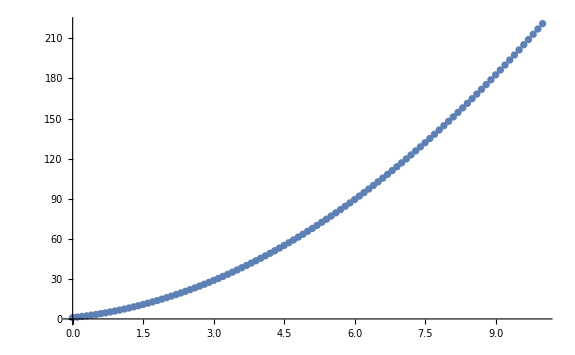

```mathematica
A=ListPlot[euler[f,0,10,100,1]]
```

```mathematica
y[t_]=x[t]/.%29
```

{1+4 t+2 t^2}

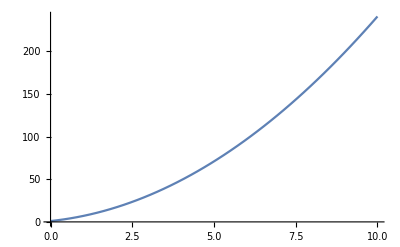

```mathematica
B=Plot[y[t],{t,0,10}]
```

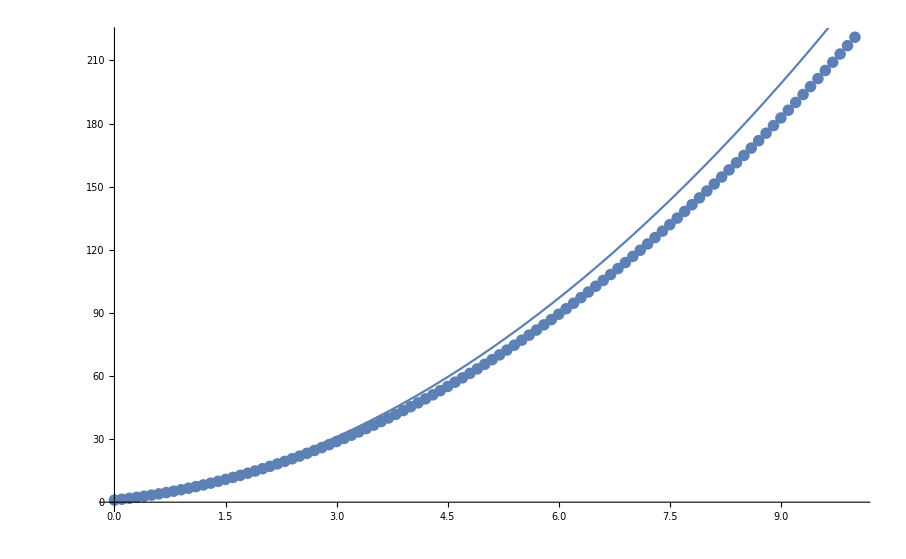

```mathematica
Show[A,B]
```